# H_0 Tension and Simple Phantom Dark Energy: Exploiting Cosmological Parameter Degeneracies - G. Alestas, L. Kazantzidis and L. Perivolaropoulos

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[NIntegrate::inumr,FindRoot::lstol];
```

### Various Constants

```mathematica
h0lcdm=67.4; 
obh2lcdm=0.0224;
om0lcdm=0.315; 
hhlcdm=h0lcdm/100;
or0lcdm=(1+3.046*7/8*(4/11)^(4/3))2.473*10^(-5);
h0riess=74.03/100;
zrec[om_,obh2_,h_]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)));
```

```mathematica
(* Planck values as given in 1502.01589 (Table 3, column 4) *)
ompl=0.3156;
σ8pl=0.831;
```

### Growth Data & MGCosmoMC Analysis

#### Import the Data

```mathematica
(* Import the Robust Growth Data from https://arxiv.org/pdf/1806.10822.pdf*)
datagrowth=Import[".\\data\\data_growth_2018_main.txt","Table"];
(* Import the chains for CMB obtained using the MGCosmoMC package *)
chain1=Import[".\\data\\wcdm12_1.txt","Table"];
chain2=Import[".\\data\\wcdm12_2.txt","Table"];
chain3=Import[".\\data\\lcdm_1.txt","Table"];
chain4=Import[".\\data\\lcdm_2.txt","Table"];
```

#### MGCosmoMC - Chains Analysis

```mathematica
(* Burn in Phase - 30% of the data should be excluded *)
MCMCchain1=chain1[[Round[0.3Length[chain1]];;-1]];
MCMCchain2=chain2[[Round[0.3Length[chain2]];;-1]];
MCMCchain3=chain3[[Round[0.3Length[chain3]];;-1]];
MCMCchain4=chain4[[Round[0.3Length[chain4]];;-1]];
```

```mathematica
(* Join the two lists *) 
MCMCwcdm=Join[MCMCchain1,MCMCchain2];
MCMClcdm=Join[MCMCchain3,MCMCchain4];
```

```mathematica
(* Position of the minimum log(L)*)
bfwcdm=MCMCwcdm[[Position[MCMCwcdm,Min[MCMCwcdm[[All,2]]]][[1,1]]]];
bflcdm=MCMClcdm[[Position[MCMClcdm,Min[MCMClcdm[[All,2]]]][[1,1]]]];
```

```mathematica
(* Actual χ^2=2 log(L) *)
chi2lcdm=2*Min[MCMClcdm[[All,2]]];
chi2wcdm=2*Min[MCMCwcdm[[All,2]]];
Print["The difference Δχ^2 for ΛCDM and wCDM with w=-1.2 is Δχ^2=",2*Min[MCMCwcdm[[All,2]]]-2*Min[MCMClcdm[[All,2]]]]
```

```mathematica
(* Positions of the two variables you want to plot. In our case we choose Subscript[Ω, 0m] and Subscript[σ, 8] *)
pp={26,30};
(* Option to obtain smoother contours *)
smoothing=0.01;
(* Obtain all the values of the two parameters from the chains *)
dataomσ8wcdm=MCMCwcdm[[All,pp]];
dataomσ8lcdm=MCMClcdm[[All,pp]];
(* Calculate the smooth kernel distribution*)
skdwcdm=SmoothKernelDistribution[dataomσ8wcdm,smoothing];
skdlcdm=SmoothKernelDistribution[dataomσ8lcdm,smoothing];
(* Calculate the probability density function *)
pdfwcdm=PDF[skdwcdm,dataomσ8wcdm];
pdflcdm=PDF[skdlcdm,dataomσ8lcdm];
contourswcdm=Quantile[pdfwcdm,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
contourslcdm=Quantile[pdflcdm,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
```

```mathematica
(* Find the best fit values for the selected parameters for ΛCDM and wCDM with w=-1.2 *)
bfwcdm=dataomσ8wcdm//Mean
bflcdm=dataomσ8lcdm//Mean
```

#### Growth Data Analysis

```mathematica
(*Formulas for calculating σ differences of terms-M corresponds to the number of free parameters*)
dchi[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig[dchi1_]:=FindRoot[dchi[nsig1]==dchi1,{nsig1,1}][[1,2]]
dchi2[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig2[dchi1_]:=FindRoot[dchi2[nsig1]==dchi1,{nsig1,3}][[1,2]]
```

```mathematica
(* Add support for WiggleZ and SDSS data Cij *)
Cijwigglez=Import[".\\data\\Cij_WiggleZ.txt","Table"];
Cijsdss=Import[".\\data\\Cij_SDSS.txt","Table"];
```

```mathematica
(* Theoretical expressions *)
δ[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=a D[Log[δ[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δ[a,w,Ω]/δ[1,w,Ω]
H[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)))
dLh[a_,om_,w_]:=2/(a √om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)])
(* Growth-rate stuff *)
amin=0.001;
Geff[a_,ga_,n_]:=1+ga(1-a)^n-ga(1-a)^(2n);
dsol[om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ]:=(dsol[om,w,ga,n]=Module[{a},NDSolve[{-((3 om d[a] Geff[a,ga,n])/(2 a^5  H[a,w,om]^2))+d'[a] (3/a+D[H[a,w,om],a]/H[a,w,om])+d''[a]==0,d[amin]==amin,d'[amin]==1},d,{a,amin,1}][[1]]])
(* The growth rate and fσ8 *)
Da[a_,om_,w_,ga_,n_]:=d[a]/.dsol[om,w,ga,n]
fa[aa_,om_,w_,ga_,n_]:=a d'[a]/d[a]/.a->aa/.dsol[om,w,ga,n]
fσ8geff[a_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,w_?NumberQ,ga_?NumberQ,n_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w,ga,n])/Da[1,om,w,ga,n] fa[aa,om,w,ga,n]/.aa->1/(1+z)
(* Corrections due to the fiducial cosmology *)
ratio[z_,w_,om_,omfid_]:=((H[a,w,om] dLh[a,om,w])/(H[a,-1,omfid] dLh[a,omfid,-1]))^(-1)/.a->1/(1+z);
```

```mathematica
Wigglez={13,14,15};
SDSS={19,20,21,22};
Cijfs81=DiagonalMatrix[datagrowth[[All,3]]^2];
Cijfs81[[Wigglez,Wigglez]]=Cijwigglez;
Cijfs81[[SDSS,SDSS]]=Cijsdss;
InvCijfs81=Inverse[Cijfs81];
(*Fiducial correction from robust paper*)
omf={0.3,0.3,0.266,0.3,0.31,0.3,0.27,0.27,0.25,0.25,0.274,0.307115,0.27,0.27,0.27,0.3,0.3,0.27,0.31,0.31,0.31,0.31};
```

```mathematica
(* χ^2 correlated term *)
vecgr[data_,w_,om_,ga_,n_,σ8_]:=Table[data[[i,2]]-ratio[data[[i,1]],w,om,omf[[i]]]fσ8geff[1/(1+data[[i,1]]),om,w,ga,n,σ8],{i,1,Length[data]}]
chi2corr[data_,w_,om_,ga_,n_,σ8_]:=vecgr[data,w,om,ga,n,σ8].InvCijfs81.vecgr[data,w,om,ga,n,σ8]
```

```mathematica
(* Planck Value for Subscript[σ, 8] *)
fmins8pl=FindMinimum[chi2corr[datagrowth,-1,om,0,1,σ8pl],{om,.3,.31}]
```

{12.6534,{om→0.235687}}

```mathematica
(* Minimize χ^2 over different parameters *)
fmwc=FindMinimum[chi2corr[datagrowth,-1,om,0,1,σ8],{om,.3,.31},{σ8,.8,.81}]
fmwc2=FindMinimum[chi2corr[datagrowth,-1.2,om,0,1,σ8],{om,.3,.31},{σ8,.8,.81}]
ombfwc=fmwc[[2,1,2]];
σ8bfwc=fmwc[[2,2,2]];
ombfwc2=fmwc2[[2,1,2]];
σ8bfwc2=fmwc2[[2,2,2]];
```

{12.2378,{om→0.256485,σ8→0.800239}}

{12.5892,{om→0.264868,σ8→0.756776}}

## Section II - CMB Spectrum Degeneracies and the H_0(w) Dependence

### h(w) for the One Parameter wCDM Model - Figure 1

```mathematica
model1[z_,w_]:=w 
deevol1=Exp[3 Integrate[(1+model1[zp,w])/(1+zp),{zp,0,z},Assumptions->z>0]];
Hwmodel1[z_,om_,or_,h_,hlcdm_,w_]:=√(om hlcdm^2 (1+z)^3+or  (1+z)^4+(h^2 -om hlcdm^2 -or )(1+z)^(3 (1+w)))
Hlcdmodel1[z_,om_,or_,h_]:=√(om h^2 (1+z)^3+or  (1+z)^4+(h^2 -om h^2 -or ))
intcmb1=NIntegrate[1/Hlcdmodel1[z,om0lcdm,or0lcdm,hhlcdm],{z,0,zrec[om0lcdm,obh2lcdm,hhlcdm]}];
intcmbw1[hh_,w_]:=NIntegrate[1/Hwmodel1[z,om0lcdm,or0lcdm,hh,hhlcdm,w],{z,0,zrec[om0lcdm,obh2lcdm,hhlcdm]}];
Part[FindRoot[intcmbw1[hh,-1.5]==intcmb1,{hh,0.7}],1,2];
```

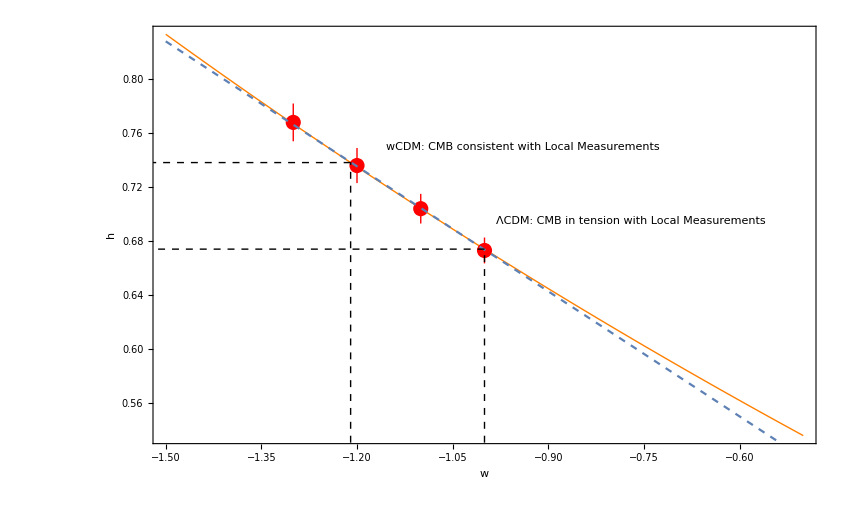

```mathematica
hfunc1[w_]:=Part[FindRoot[intcmbw1[hh,w]==intcmb1,{hh,0.7}],1,2]
approxline=-0.309x+0.3646==0;
plapprox=Plot[approxline,{x,-1.5,-0.5},PlotRange->All,PlotStyle->Dashed];
plH0bf=ListPlot[{{-1,Around[0.673,0.0096]},{-1.1,Around[0.704,0.011]},{-1.2,Around[0.736,0.013]},{-1.3,Around[0.768,0.014]}},PlotStyle->{Red}];
pl0=Plot[hfunc1[w],{w,-1.5,-0.5},Frame->True,FrameLabel->{"w","h"},BaseStyle -> {FontFamily->"Times",13},PlotStyle->{Orange,Thick}];
pl1=Show[pl0,plH0bf,pltest,Graphics[{Dashed,Line[{{-1,0},{-1,0.674}}]}],Graphics[{Dashed,Line[{{-1,0.674},{-1.55,0.674}}]}],
Graphics[{Dashed,Line[{{-1.21,0.7382},{-1.55,0.7382}}]}],
Graphics[{Dashed,Line[{{-1.21,0},{-1.21,0.7382}}]}],
Graphics[{Inset["ΛCDM: CMB in tension with Local Measurements",{-0.77,0.695}]}],
Graphics[{Inset["wCDM: CMB consistent with Local Measurements",{-0.94,0.75}]}],BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->850]
```

```mathematica
Export["H_w_wcdm.pdf",pl1,ImageResolution->1000,ImageSize->850]
```

H_w_wcdm.pdf

### wCPL Contour Plot - Figure 3

```mathematica
model2[z_,w0_,w1_]:=w0+w1 z/(z+1)
deevol2=Exp[3 Integrate[(1+model2[zp,w0,w1])/(1+zp),{zp,0,z},Assumptions->z>0]];
hfunc2[w0_,w1_]:=Part[FindRoot[intcmbw2[hh,w0,w1]==intcmb2,{hh,0.7}],1,2]//Chop
Hwmodel2[z_,om_,or_,h_,hlcdm_,w0_,w1_]:=√(om hlcdm^2 (1+z)^3+or  (1+z)^4+(h^2 -om hlcdm^2 -or )ⅇ^(3 (-(w1 z)/(1+z)+(1+w0+w1) Log[1+z])))
Hlcdmodel2[z_,om_,or_,h_]:=√(om h^2 (1+z)^3+or  (1+z)^4+(h^2 -om h^2 -or ))
intcmb2=NIntegrate[1/Hlcdmodel2[z,om0lcdm,or0lcdm,hhlcdm],{z,0,zrec[om0lcdm,obh2lcdm,hhlcdm]}];
intcmbw2[hh_,w0_,w1_]:=NIntegrate[1/Hwmodel2[z,om0lcdm,or0lcdm,hh,hhlcdm,w0,w1],{z,0,zrec[om0lcdm,obh2lcdm,hhlcdm]}];
Part[FindRoot[intcmbw2[hh,-1.1,-0.1]==intcmb2,{hh,0.7}],1,2];
```

```mathematica
pl3=ContourPlot[hfunc2[w0,w1],{w0,-1.3,-0.9},{w1,-0.6,0.2},Contours->{{0.7403,{Dashed,Black}},{0.674,{Dashed,Black}},##&@@({#,None}&/@Range[0.62,0.8,.02])},FrameLabel->{"w_0","w_1"},BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],PlotLegends->Automatic,ColorFunction->"TemperatureMap"];
```

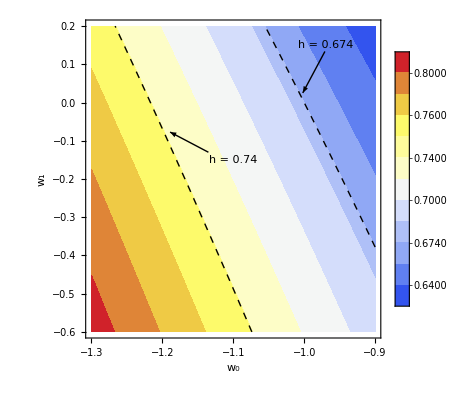

```mathematica
pl3tot=Show[pl3,Graphics[{Inset["h = 0.674",{-0.97,0.15}]}],Graphics[{Inset["h = 0.74",{-1.1,-0.15}]}],Graphics[Arrow[{{-0.9708,0.1337},{-1.002,0.02522}}]],Graphics[Arrow[{{-1.135,-0.13},{-1.189,-0.07724}}]]]
```

```mathematica
Export["H_w_cpl.pdf",pl3tot,ImageResolution->1000,ImageSize->850]
```

H_w_cpl.pdf

```mathematica
(*Linear Fit approximation of the contour lines of fig. 3*)
listfitriess={{-1.246,0.1203},{-1.122,-0.3969}};
listfitlcdm={{-1.019,0.06905},{-0.9457,-0.2027}};
LinearModelFit[listfitriess,x,x]
LinearModelFit[listfitlcdm,x,x]
```

### Evolution of w(z) - Figure 4

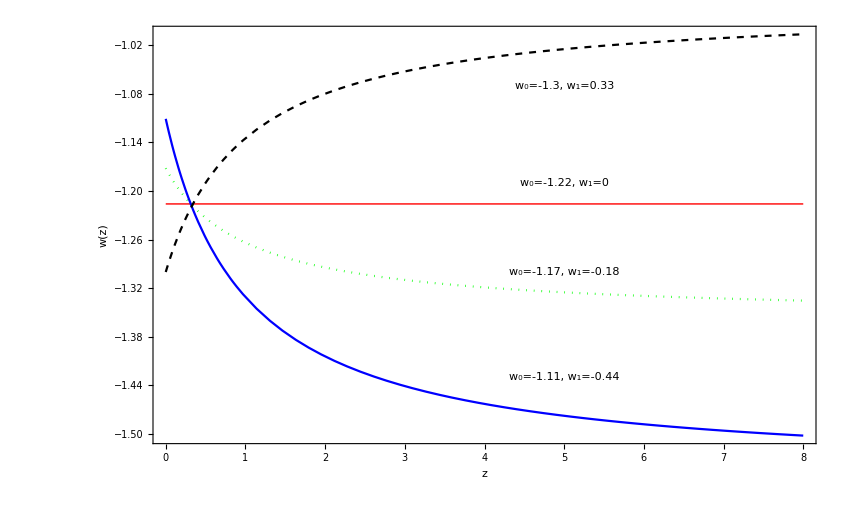

```mathematica
w[z_,ww0_,ww1_]:= ww0+ww1 z/(1+z);
plw1=Plot[w[z,-1.216,0],{z,0,8},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"z","w(z)"},BaseStyle->{FontFamily->"Times",25},FrameStyle->Directive[Black]];
plw2=Plot[w[z,-1.172,-0.1837],{z,0,8},PlotStyle->{Green,Dotted}];
plw3=Plot[w[z,-1.2,-0.06575],{z,0,8},PlotStyle->{Black,Dashed}];
plw4=Plot[w[z,-1.111,-0.4397],{z,0,8},PlotStyle->Blue];
plw5=Plot[w[z,-1.3,0.33],{z,0,8},PlotStyle->{Black,Dashed}];
plwtot=Show[plw1,plw2,plw4,plw5,PlotRange->{-1,-1.5},ImageSize->850,Epilog->{Text["w_0=-1.22, w_1=0",{5,-1.19}],Text["w_0=-1.17, w_1=-0.18",{5,-1.3}],Text["w_0=-1.11, w_1=-0.44",{5,-1.43}],,Text["w_0=-1.3, w_1=0.33",{5,-1.07}]}]
```

```mathematica
Export["wcpl_line.pdf",plwtot,ImageResolution->1000,ImageSize->850]
```

wcpl_line.pdf

```mathematica
(*Point of intersection*)
NSolve[w[z,-1.1,-0.487]==w[z,-1.172,-0.1837],z]
```

{{z→0.311284}}

## Section III - Numerical Analysis of Dark Energy Models

### 1σ - 4σ Contours in the Ω_m-σ_8 Parametric Space - Figure 6

```mathematica
(* CMB contours *)
wcdmcontour=ContourPlot[PDF[skdwcdm,{a,b}],{a, 0.15, 0.35},{b,.8,0.95},Contours->contourswcdm,ContourShading->False, ContourStyle->Red,FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bfwcdm[[1]],bfwcdm[[2]]}]}}];
lcdmcontour=ContourPlot[PDF[skdlcdm,{a,b}],{a, 0.1, 0.4},{b,.7,0.95},Contours->contourswcdm,ContourShading->False, ContourStyle->Red,FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bflcdm[[1]],bflcdm[[2]]}]}}];
```

```mathematica
(* Growth contours for ΛCDM *)
cont1s2s3s4somσ8=ContourPlot[chi2corr[datagrowth,-1,om,0,1,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc[[1]]+dchi[1],fmwc[[1]]+dchi[2],fmwc[[1]]+dchi[3],fmwc[[1]]+dchi[4]},ContourShading->False,ContourStyle->Blue,ContourStyle->{Hue[0.6,.9,.9],Hue[0.6,.6,.9],Hue[0.6,.2,.9],White}];
```

```mathematica
(* Overlap the CMB and growth contours for ΛCDM *)
cont1=Show[{cont1s2s3s4somσ8,lcdmcontour},FrameLabel->{"Ω_(0  m)","σ_8"},Epilog->{{PointSize[Medium],Green,Point[{ombfwc,σ8bfwc}]},
{PointSize[Medium],Black,Point[{bflcdm[[1]],bflcdm[[2]]}]},Text["fσ_8 Likelihood Contours for w=-1",{0.42,0.6}],Text["CMB Best-fit for w=-1",{0.51,0.87}]},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Medium];
```

```mathematica
(* Growth contours for wCDM with w=-1.2 *)
cont1s2s3s4somσ8w=ContourPlot[chi2corr[datagrowth,-1.2,om,0,1,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc2[[1]]+dchi[1],fmwc2[[1]]+dchi[2],fmwc2[[1]]+dchi[3],fmwc2[[1]]+dchi[4]},ContourShading->False,ContourStyle->Blue];
```

```mathematica
(* Overlap the CMB and growth contours for wCDM with w=-1.2 *)
cont2=Show[{cont1s2s3s4somσ8w,wcdmcontour},Epilog->{{PointSize[Medium],Green,Point[{ombfwc2,σ8bfwc2}]},
{PointSize[Medium],Black,Point[{bfwcdm[[1]],bfwcdm[[2]]}]},Text["fσ_8 Likelihood Contours for w=-1.2",{0.42,0.6}],Text["CMB Best-fit for w=-1.2",{0.49,0.88}]},FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",18},FrameStyle->Directive[Black],ImageSize->Medium];
```

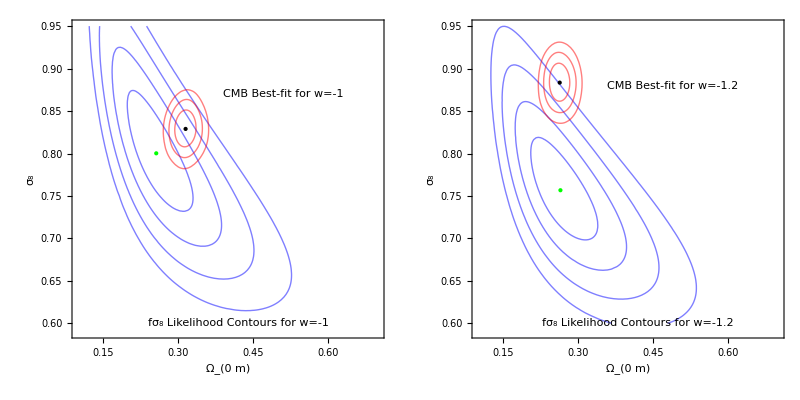

```mathematica
fig5=GraphicsGrid[{{cont1,cont2}},Spacings->0,ImageSize->800]
```

```mathematica
Export[NotebookDirectory[]<>"Growth_CMB.pdf",fig5,ImageResolution->1000];
```